```mathematica
Get["/Users/beto/Documents/Wolfram Mathematica/Base/Alpha/Alpha.m"]
```

```mathematica
cm16 = {{0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0}, 
        {0, 0, 1, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 1},
        {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 1, 0},
        {1, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0},
        {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0}, 
        {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0},
        {0, 0, 0, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 0, 1},
        {1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0},
        {0, 0, 1, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 1, 1, 0}, 
        {1, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 1, 0}, 
        {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1},
        {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1, 0},
        {0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0},
        {0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0},
        {1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0},
        {0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0}};

dyn16 = {"AND", "OR", "OR", "AND", "OR", "OR", "AND", "OR", "OR", 
   "AND", "OR", "OR", "AND", "AND", "OR", "AND"};

res16 =findIndexesOfOutputs4Mechanism[{5, 7, 9, 10}, {0, 0, 1, 0}, dyn16, cm16];
```

```mathematica
gp=givePlaces[res16["DecimalRepertoire"],res16["Sumandos"]];
```

```mathematica
cm05 = {{0, 1, 1, 1, 1}, {1, 1, 1, 0, 0}, {1, 0, 0, 1, 0}, {1, 1, 0, 
    0, 0}, {0, 1, 1, 1, 0}};
dyn05 = {"AND", "AND", "OR", "AND", "OR"};

fullRep = runDynamic[cm05, dyn05]

ff05 = calculatingPattsInDivisionsOfCM[cm05, dyn05, 2];
locations05 = ff05["Locations"];
sumandos05 = ff05["Sumandos"];
(*ByteCount[ff05]*)

cca05 = calculatingAttractors[locations05, sumandos05]
```

<|RepertoireOutputs→{{0,0,0,0,0},{0,0,1,0,0},{0,0,0,0,1},{0,0,1,1,1},{0,0,0,0,1},{0,0,1,0,1},{0,0,0,0,1},{0,1,1,1,1},{0,0,1,0,1},{0,0,1,0,1},{0,0,1,0,1},{0,0,1,1,1},{0,0,1,0,1},{0,0,1,0,1},{0,0,1,0,1},{0,1,1,1,1},{0,0,0,0,0},{0,0,1,0,0},{0,0,0,0,1},{0,0,1,1,1},{0,0,0,0,1},{0,0,1,0,1},{0,0,0,0,1},{0,1,1,1,1},{0,0,1,0,1},{0,0,1,0,1},{0,0,1,0,1},{0,0,1,1,1},{0,0,1,0,1},{0,0,1,0,1},{1,0,1,0,1},{1,1,1,1,1}}|>

<|AttractorsByPosition→<|0→{0,16},4→{1,17},16→{2,4,6,18,20,22},20→{5,8,9,10,12,13,14,21,24,25,26,28,29},21→{30},28→{3,11,19,27},30→{7,15,23},31→{31}|>|>

```mathematica
response = findIndexesOfOutputs4Mechanism[{1,2,3,4,5}, {0,0,0,0,0}, dyn05, cm05]
```

<|AllInputNodes→{2,3,4,5,1},DecimalRepertoire→{0,16},Sumandos→{0}|>

```mathematica
givePlaces[response["DecimalRepertoire"],response["Sumandos"]]
```

{0,16}

## Creating Random Dynamics

```mathematica
Get["/Users/beto/Documents/Wolfram Mathematica/Base/Alpha/Alpha.m"]
createSimpleRandomDynamic[12]["Dynamic"]
```

{OR,OR,OR,OR,OR,AND,AND,AND,OR,AND,OR,OR}

```mathematica
generateStringList[4]
```

(1,2,3,4)

## Generate files for pyphi

### Definition of limits

```mathematica
numberNetworks  = 5;
noNodes = 8;
noEdges = 2;
outDir ="/Users/beto/Documents/DOCTORADO_2025/EXPERIMENTS/";
```

### Creation of files

```mathematica
For [i=1,i≤numberNetworks,i++,

ranGraph=RandomGraph[BarabasiAlbertGraphDistribution[noNodes,noEdges]];
dyn=createSimpleRandomDynamic[noNodes]["Dynamic"];
adjMat=AdjacencyMatrix[ranGraph]//Normal;
outRep = runDynamic[adjMat,dyn]["RepertoireOutputs"];
oneInput=createBinRandomInput[Length[adjMat]];
oneOut=calculateOneOutptuOfNetwork[input,cm,dyn]["Output"];
]
```

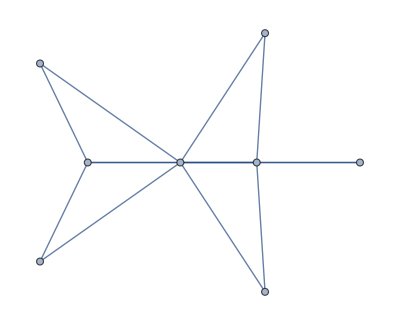

{OR,OR,AND,OR,AND,OR,OR,AND}

{{0,1,1,1,1,1,1,1},{1,0,1,1,1,1,0,0},{1,1,0,0,0,0,1,1},{1,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,0,1,0,0,0,0,0}}

{1,1,0,0,0,1,1,0}

{1,1,1,1,1,1,1,1}

```mathematica
ranGraph
dyn
adjMat
(*outRep*)
oneInput
oneOut
```

```mathematica
Get["/Users/beto/Documents/Wolfram Mathematica/Base/Alpha/Alpha.m"]


cm05 = {{0, 1, 1, 1, 1}, {1, 1, 1, 0, 0}, {1, 0, 0, 1, 0}, {1, 1, 0, 
    0, 0}, {0, 1, 1, 1, 0}};
dyn05 = {"AND", "AND", "OR", "AND", "OR"};

ff05 = calculatingPattsInDivisionsOfCM[cm05, dyn05, 2]
locations05 = ff05["Locations"];
sumandos05 = ff05["Sumandos"];
(*ByteCount[ff05]*)
```

<|Locations→{<|{0,0}→{0,1,2,3,4,5,6,8,9,10,11,12,13,14,16,17,18,19,20,21,22,24,25,26,27,28,29},{1,0}→{30},{0,1}→{7,15,23},{1,1}→{31}|>,<|{0,0}→{0,2},{1,0}→{1,8,10,9},{1,1}→{3,11}|>,<|{0}→{0},{1}→{2,4,6,8,10,12,14}|>},Sumandos→{<|{0,0}→{0},{1,0}→{0},{0,1}→{0},{1,1}→{0}|>,<|{0,0}→{0,4,16,20},{1,0}→{0,4,16,20},{1,1}→{0,4,16,20}|>,<|{0}→{0,1,16,17},{1}→{0,1,16,17}|>}|>

```mathematica
cca05 = calculatingAttractors[locations05, sumandos05]
```

<|DecAttractorsByPosition→<|0→{0,16},4→{1,17},16→{2,4,6,18,20,22},20→{5,8,9,10,12,13,14,21,24,25,26,28,29},21→{30},28→{3,11,19,27},30→{7,15,23},31→{31}|>,BinAttractorsByPosition→<|{0,0,0,0,0}→{0,16},{0,0,0,0,1}→{2,4,6,18,20,22},{0,0,1,0,0}→{1,17},{0,0,1,0,1}→{5,8,9,10,12,13,14,21,24,25,26,28,29},{0,0,1,1,1}→{3,11,19,27},{1,0,1,0,1}→{30},{0,1,1,1,1}→{7,15,23},{1,1,1,1,1}→{31}|>|>

```mathematica
onPossibleBehaviour[{1,2,3,4,5},{0,0,0,0,0}, dyn05, cm05]
```

<|DecimalRepertoire→{0,16},Sumandos→{0}|>

# MY PHI

```mathematica
(*Define the main function*)generateNetworkData[maxNodes_]:=Module[{networks,nodeSize,noEdges,ranGraph,adjMat,dyn,outRep,oneInput,oneOut,ff,binAttractors,k0,a0,sensitivities,phiK,rules0,kRule0,rules1,kRule1,deltaKRule,phiKRefined,csvData},(*Initialize variables*)networks={};
If[maxNodes===Null||!NumericQ[maxNodes],maxNodes=12;
Print["maxNodes set to default: 12"];];

(*Loop over node sizes*)
Do[
nodeSize=n;
Print["Processing nodeSize: ",nodeSize];
noEdges=RandomInteger[{Floor[n/2],Floor[(n*(n-1))/2]}];

(*Loop over graph types*)
Do[
ranGraph=Switch[type,
"BA",RandomGraph[BarabasiAlbertGraphDistribution[nodeSize,noEdges]],
"WS",RandomGraph[WattsStrogatzGraphDistribution[nodeSize,0.3]],
"Ring",CycleGraph[nodeSize],
"Complete",CompleteGraph[nodeSize]];

(*Calculate adjacency matrix and dynamics*)
adjMat=Normal[AdjacencyMatrix[ranGraph]];
dyn=createSimpleRandomDynamic[nodeSize]["Dynamic"];
outRep=runDynamic[adjMat,dyn]["RepertoireOutputs"];
oneInput=createBinRandomInput[nodeSize];
oneOut=calculateOneOutptuOfNetwork[oneInput,adjMat,dyn]["Output"];
ff=calculatingPattsInDivisionsOfCM[adjMat,dyn,2];
binAttractors=calculatingAttractors[ff["Locations"],ff["Sumandos"]]["BinAttractorsByPosition"];

(*Calculate sensitivities*)
k0=ByteCount[binAttractors];
a0=Length[binAttractors];
sensitivities=Select[Flatten[Table[Module[{adjMatPert=adjMat,ffPert,binAttPert,k1,a1,deltaK,deltaA},If[adjMat[[i,j]]==1,adjMatPert[[i,j]]=0;
ffPert=calculatingPattsInDivisionsOfCM[adjMatPert,dyn,2];
binAttPert=calculatingAttractors[ffPert["Locations"],ffPert["Sumandos"]]["BinAttractorsByPosition"];

(*Check if binAttPert is valid*)
If[
AssociationQ[binAttPert],
k1=ByteCount[binAttPert];
a1=Length[binAttPert];
deltaK=Abs[k0-k1];
deltaA=Abs[a0-a1];
deltaK Log[2,deltaA+1],0],0]]
,{i,nodeSize},{j,nodeSize}]],#>0&];

(*Calculate phiK*)
phiK=If[Length[sensitivities]>0,Mean[sensitivities],0];

(*Calculate rules and refined phiK*)rules0=(onPossibleBehaviour[Range[nodeSize],#,dyn,adjMat]&)/@Keys[binAttractors];
kRule0=Mean[ByteCount/@rules0];
rules1=Module[{adjMatPert=adjMat},If[adjMat[[1,2]]==1,adjMatPert[[1,2]]=0];
(onPossibleBehaviour[Range[nodeSize],#,dyn,adjMatPert]&)/@Keys[binAttPert]]/@Keys[binAttractors];
kRule1=Mean[ByteCount/@rules1];
deltaKRule=Abs[kRule0-kRule1];
phiKRefined=N[phiK+deltaKRule](*Convert to numerical value*)

(*Prepare CSV data*)
csvData={nodeSize,StringReplace[ToString[outRep,InputForm],{"{"->"[","}"->"]"}],StringReplace[ToString[adjMat,InputForm],{"{"->"[","}"->"]"}],StringReplace[ToString[oneOut,InputForm],{"{"->"[","}"->"]"}],ToString[dyn],(*Add dynamics to CSV data*)phiKRefined};
(*Append to networks list*)
AppendTo[networks,csvData];,{type,{"BA","WS","Ring","Complete"}}];,{n,5,maxNodes}];

(*Export to CSV*)
Export["/Users/beto/Documents/DOCTORADO_2025/EXPERIMENTS/network_data.csv",Prepend[networks,{"NumberOfNodes","OutputRepertoire","AdjacencyMatrix","OneOutput","Dynamics","PhiK"}],"CSV"];];

(*Run the main function*)
generateNetworkData[9];
```

Processing nodeSize: 5

Keys::invrl: The argument binAttPert is not a valid Association or a list of rules.

Part::partd: Part specification binAttPert⟦1⟧ is longer than depth of object.

Part::partd: Part specification binAttPert⟦2⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part {1,2,3,4} of {0} does not exist.

Part::partw: Part {1,2,3,4} of {1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification binAttPert⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Processing nodeSize: 6

Processing nodeSize: 7

Processing nodeSize: 8

Processing nodeSize: 9

## Plotting networks

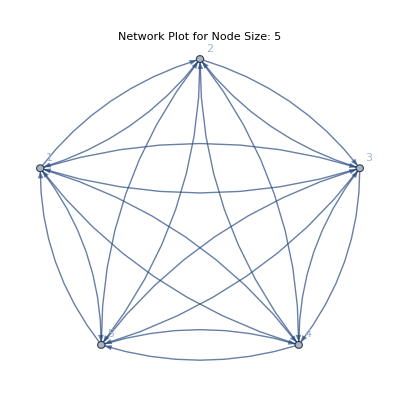
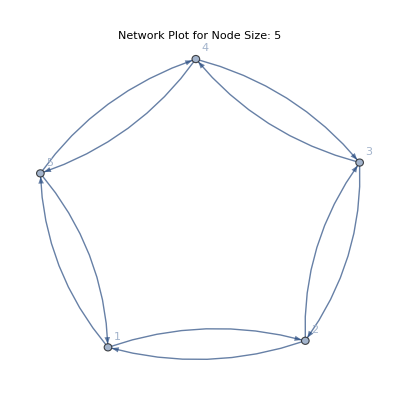
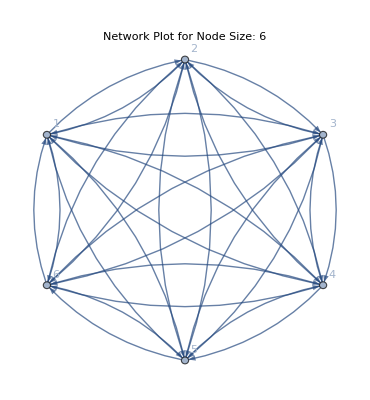
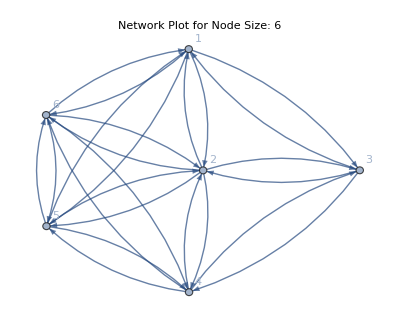
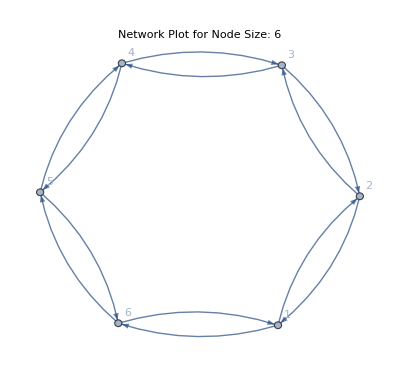
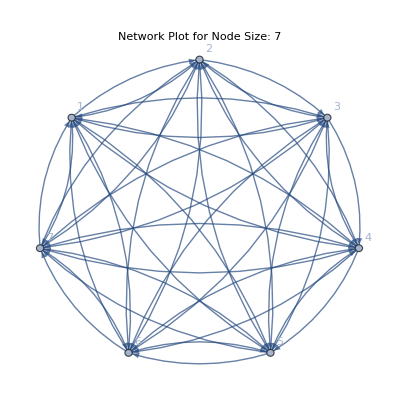
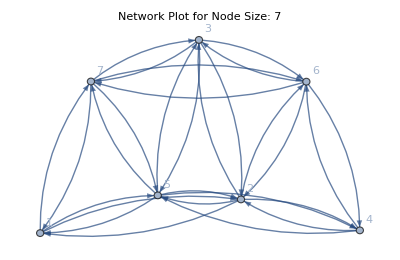
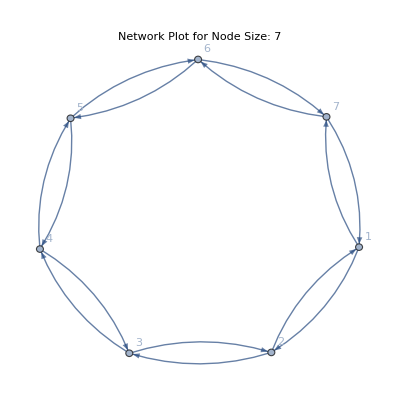
{-Graphics- | 
(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, OR, AND, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, OR, AND, AND} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, OR, AND, AND, AND} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, AND, OR, AND, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, OR, AND, OR, OR, OR} | ,-Graphics- | 
(0 | 1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, OR, OR, AND, OR} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, AND, OR, AND, AND, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, OR, OR, OR, OR, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, AND, AND, AND, AND, AND} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, OR, OR, AND, AND, AND, OR} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, OR, AND, AND, AND, OR, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, AND, AND, AND, AND, AND, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, AND, OR, AND, OR, OR, AND} | ,-Graphics- | 
(0 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, AND, OR, OR, OR, AND, OR, AND} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, OR, AND, AND, OR, AND, AND} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, AND, OR, AND, OR, OR, OR} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, OR, AND, AND, OR, OR, AND, OR} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, AND, AND, OR, OR, OR, OR, OR} | ,-Graphics- | 
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | Adjacency Matrix
Dynamics: {OR, AND, OR, OR, OR, AND, AND, OR, AND} | ,-Graphics- | 
(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0) | Adjacency Matrix
Dynamics: {AND, AND, OR, AND, AND, AND, AND, AND, AND} | }

```mathematica
(*Function to convert string representation of a matrix to a Mathematica matrix*)stringToMatrix[matrixString_]:=Module[{matrix},matrix=ToExpression[StringReplace[matrixString,{"["->"{","]"->"}"}]];
Return[matrix];]

(*Read the CSV file*)
data=Import["/Users/beto/Documents/DOCTORADO_2025/EXPERIMENTS/network_data.csv"];

(*Extract headers*)
headers=First[data];

(*Extract the adjacency matrix and dynamics column indices*)
adjMatrixColumnIndex=Position[headers,"AdjacencyMatrix"][[1,1]];
dynColumnIndex=Position[headers,"Dynamics"][[1,1]];

(*Function to plot the network,display the adjacency matrix,and dynamics from a row of data*)
plotNetworkFromRow[row_]:=Module[{adjMatrixString,adjMatrix,dynString,nodeSize},adjMatrixString=row[[adjMatrixColumnIndex]];
dynString=row[[dynColumnIndex]];
nodeSize=row[[1]];
adjMatrix=stringToMatrix[adjMatrixString];
Grid[{{AdjacencyGraph[adjMatrix,DirectedEdges->True,VertexLabels->"Name",PlotLabel->"Network Plot for Node Size: "<>ToString[nodeSize]],SpanFromLeft},{MatrixForm[adjMatrix],Style["Adjacency Matrix",Bold,FontSize->12]},{Style["Dynamics: "<>dynString,Bold,FontSize->12]}}]]

(*Plot the network,display the adjacency matrix,and dynamics for each row in the data*)
Table[plotNetworkFromRow[data[[i]]],{i,2,Length[data]}]
```

# Revisited version

```mathematica
Get["/Users/beto/Documents/Wolfram Mathematica/Base/Alpha/Alpha.m"]
```

```mathematica
generateNetworkData[maxNodes_]:=Module[{networks,nodeSize,noEdges,ranGraph,adjMat,dyn,outRep,oneInput,oneOut,ff,binAttractors,k0,a0,sensitivities,phiK,rules0,kRule0,rules1,kRule1,deltaKRule,phiKRefined,csvData},(*Initialize variables*)networks={};
(*Check if maxNodes is valid;if not,set a default value of 12 for consistency*)If[maxNodes===Null||!NumericQ[maxNodes],maxNodes=12;
Print["maxNodes set to default: 12"]];
(*Loop over node sizes*)Do[nodeSize=n;
Print["Processing nodeSize: ",nodeSize];
(*Randomly select number of edges between minimum (n/2) and maximum (n*(n-1)/2) to simulate varying connectivity*)noEdges=RandomInteger[{Floor[n/2],Floor[(n*(n-1))/2]}];
(*Loop over graph types*)Do[(*Use Switch to generate a random graph based on type,inspired by real-world network models*)ranGraph=Switch[type,"BA",RandomGraph[BarabasiAlbertGraphDistribution[nodeSize,noEdges]],"WS",RandomGraph[WattsStrogatzGraphDistribution[nodeSize,0.3]],"Ring",CycleGraph[nodeSize],"Complete",CompleteGraph[nodeSize]];
(*Calculate adjacency matrix and dynamics*)adjMat=Normal[AdjacencyMatrix[ranGraph]];
dyn=createSimpleRandomDynamic[nodeSize]["Dynamic"];
outRep=runDynamic[adjMat,dyn]["RepertoireOutputs"];
oneInput=createBinRandomInput[nodeSize];
oneOut=calculateOneOutptuOfNetwork[oneInput,adjMat,dyn]["Output"];
ff=calculatingPattsInDivisionsOfCM[adjMat,dyn,2];
binAttractors=calculatingAttractors[ff["Locations"],ff["Sumandos"]]["BinAttractorsByPosition"];
(*Calculate sensitivities*)k0=ByteCount[binAttractors];
a0=Length[binAttractors];
(*Compute sensitivities for each edge perturbation*)sensitivities=Select[Flatten[Table[Module[{adjMatPert=adjMat,ffPert,binAttPert,k1,a1,deltaK,deltaA},If[adjMat[[i,j]]==1,adjMatPert[[i,j]]=0;
ffPert=calculatingPattsInDivisionsOfCM[adjMatPert,dyn,2];
binAttPert=calculatingAttractors[ffPert["Locations"],ffPert["Sumandos"]]["BinAttractorsByPosition"];
(*Check if binAttPert is a valid association*)If[AssociationQ[binAttPert],k1=ByteCount[binAttPert];
a1=Length[binAttPert];
deltaK=Abs[k0-k1];
deltaA=Abs[a0-a1];
deltaK Log[2,deltaA+1],0],0]],{i,nodeSize},{j,nodeSize}]],#>0&];
(*Calculate phiK*)phiK=If[Length[sensitivities]>0,Mean[sensitivities],0];
(*Calculate rules and refined phiK*)rules0=(onPossibleBehaviour[Range[nodeSize],#,dyn,adjMat]&)/@Keys[binAttractors];
kRule0=Mean[ByteCount/@rules0];
(*Fix rules1 calculation*)rules1=Module[{adjMatPert=adjMat},If[adjMat[[1,2]]==1,adjMatPert[[1,2]]=0];
(onPossibleBehaviour[Range[nodeSize],#,dyn,adjMatPert]&)/@Keys[binAttractors]];
kRule1=Mean[ByteCount/@rules1];
deltaKRule=Abs[kRule0-kRule1];
phiKRefined=N[phiK+deltaKRule];
(*Prepare CSV data*)csvData={nodeSize,StringReplace[ToString[outRep,InputForm],{"{"->"[","}"->"]"}],StringReplace[ToString[adjMat,InputForm],{"{"->"[","}"->"]"}],StringReplace[ToString[oneOut,InputForm],{"{"->"[","}"->"]"}],ToString[dyn],phiKRefined};
(*Append to networks list*)AppendTo[networks,csvData];,{type,{"BA","WS","Ring","Complete"}}];,{n,5,maxNodes}];
(*Export to CSV*)Export["/Users/beto/Documents/DOCTORADO_2025/EXPERIMENTS/network_data.csv",Prepend[networks,{"NumberOfNodes","OutputRepertoire","AdjacencyMatrix","OneOutput","Dynamics","PhiK"}],"CSV"];]
```

## Execution

```mathematica
generateNetworkData[9]
```

Processing nodeSize: 5

Processing nodeSize: 6

Processing nodeSize: 7

Processing nodeSize: 8

Processing nodeSize: 9